=== TESTING phaseSpace2D ===

Testing with 2D competition model...

Creating phase space analysis with parameters: {}

Phase space analysis completed:

Number of trajectories: 6

Number of unique attractors: 1

Attractor locations (I1, I2): {{1.,0.}}

Test completed. Displaying phase portrait:

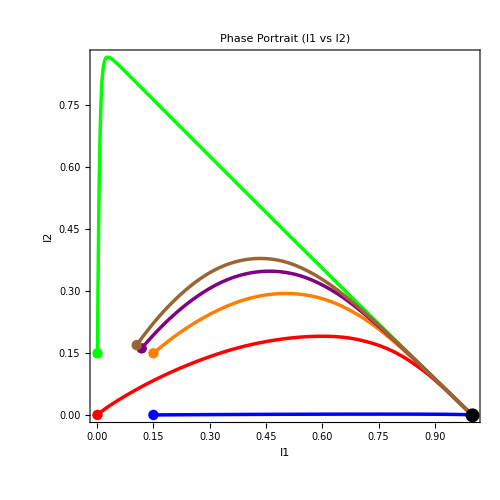

Test summary:

Number of attractors found: 1

Attractor locations: {{0.999999,1.15118×10^-6}}

=== TESTING with parameters ===

Testing with parameterized 2D competition model...

Creating phase space analysis with parameters: {a1=1.,a2=0.9,b12=0.8,b21=1.2}

Phase space analysis completed:

Number of trajectories: 6

Number of unique attractors: 2

Attractor locations (I1, I2): {{1.,0.},{0.987,0.013}}

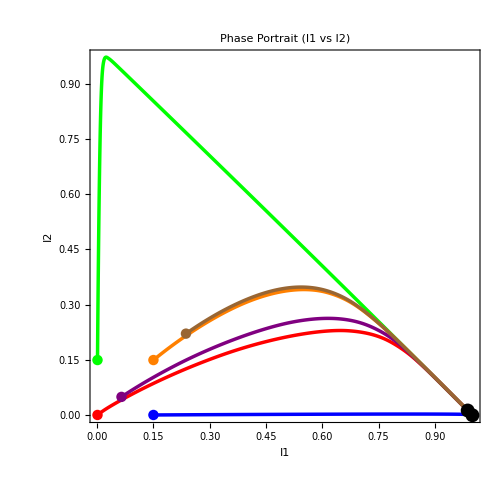

```mathematica
(*EXECUTE THIS FIRST:*)Clear[phaseSpace2D]

(*2D Phase Space Analysis-creates phase portrait and analyzes dynamics*)
phaseSpace2D[RHS_,var_,par_,paramValues_,tMax_:200,nInitials_:8]:=Block[{maxSteps=25000,ndsMethod="StiffnessSwitching",conPar,rhsWithParams,rhsWithFunctions,initialConditions,trajectories,tsol,ic,icSet,odeSystem,initialCondSystem,I1Index,I2Index,I1samples,I2samples,sampleTimes,phasePortrait,trajectory,allTrajectories,colors,analysisTime,meanI1,meanI2,amplitudeI1,amplitudeI2,finalValues,attractors,uniqueAttractors,tol,attractorColors,attractorPlot,combinedPlot},(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
(*Set parameters*)conPar=Thread[par->paramValues];
rhsWithParams=RHS/. conPar;
rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
tol=10^(-3);
Print["Creating phase space analysis with parameters: ",Table[ToString[par[[i]]]<>"="<>ToString[paramValues[[i]]],{i,1,Min[4,Length[par]]}]];
(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like*)icSet=Table[0.01,{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like*)icSet=Table[0.01,{Length[var]}];
icSet[[I1Index]]=0.15;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like*)icSet=Table[0.01,{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.15;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like*)icSet=Table[0.01,{Length[var]}];
icSet[[I1Index]]=0.15;
icSet[[I2Index]]=0.15;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[RandomReal[{0.001,0.25}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
(*Colors for different trajectories*)colors={Red,Blue,Green,Orange,Purple,Brown,Pink,Cyan};
(*Run simulations from different initial conditions*)allTrajectories={};
attractors={};
Do[ic=initialConditions[[k]];
odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax},Method->ndsMethod,MaxSteps->maxSteps]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,(*Extract trajectory data*)sampleTimes=Table[t,{t,0,tMax,tMax/1000}];
I1samples=Table[I1[t]/. tsol[[1]],{t,sampleTimes}];
I2samples=Table[I2[t]/. tsol[[1]],{t,sampleTimes}];
trajectory=Transpose[{I1samples,I2samples}];
AppendTo[allTrajectories,{trajectory,colors[[Mod[k-1,Length[colors]]+1]]}];
(*Store final point as potential attractor*)finalValues={I1[tMax]/. tsol[[1]],I2[tMax]/. tsol[[1]]};
If[AllTrue[finalValues,#>=0&],AppendTo[attractors,finalValues];];];,{k,1,Length[initialConditions]}];
(*Find unique attractors*)If[Length[attractors]>0,uniqueAttractors={attractors[[1]]};
Do[If[Min[Table[Max[Abs[attractors[[i]]-uniqueAttractors[[j]]]],{j,1,Length[uniqueAttractors]}]]>tol,AppendTo[uniqueAttractors,attractors[[i]]];];,{i,2,Length[attractors]}];,uniqueAttractors={};];
(*Create phase portrait*)If[Length[allTrajectories]>0,phasePortrait=Graphics[{(*Trajectories*)Table[{allTrajectories[[i,2]],Thickness[0.005],Line[allTrajectories[[i,1]]]},{i,1,Length[allTrajectories]}],(*Initial conditions as small circles*)Table[{allTrajectories[[i,2]],PointSize[0.015],Point[allTrajectories[[i,1,1]]]},{i,1,Length[allTrajectories]}]},Frame->True,FrameLabel->{"I1","I2"},PlotLabel->"Phase Portrait (I1 vs I2)",AspectRatio->1,ImageSize->500,PlotRange->All];
(*Add attractors if they exist*)If[Length[uniqueAttractors]>0,attractorColors=Table[Black,{Length[uniqueAttractors]}];
attractorPlot=Graphics[{Black,PointSize[0.02],Point[uniqueAttractors]}];
combinedPlot=Show[phasePortrait,attractorPlot];,combinedPlot=phasePortrait;];
(*Print analysis*)Print["Phase space analysis completed:"];
Print["Number of trajectories: ",Length[allTrajectories]];
Print["Number of unique attractors: ",Length[uniqueAttractors]];
If[Length[uniqueAttractors]>0,Print["Attractor locations (I1, I2): ",Table[{Round[uniqueAttractors[[i,1]],0.001],Round[uniqueAttractors[[i,2]],0.001]},{i,1,Length[uniqueAttractors]}]];];
(*Return results*)<|"PhasePortrait"->combinedPlot,"Trajectories"->allTrajectories,"Attractors"->uniqueAttractors,"ParameterValues"->paramValues|>,(*No successful trajectories*)Print["No successful trajectories found"];
<|"PhasePortrait"->Graphics[],"Trajectories"->{},"Attractors"->{},"ParameterValues"->paramValues|>]];

(*TEST CASE*)
Print["=== TESTING phaseSpace2D ==="];

(*Define a simple 2D competition model*)
testRHS={I1*(1-I1-0.8*I2),I2*(0.9-I2-1.2*I1)};

testVar={I1,I2};
testPar={};  (*No parameters in this simple case*)
testParamValues={};  (*No parameter values*)

(*Run test*)
Print["Testing with 2D competition model..."];
testResult=phaseSpace2D[testRHS,testVar,testPar,testParamValues,50,6];

(*Display results*)
Print["Test completed. Displaying phase portrait:"];
testResult["PhasePortrait"]

(*Print test summary*)
Print["Test summary:"];
Print["Number of attractors found: ",Length[testResult["Attractors"]]];
Print["Attractor locations: ",testResult["Attractors"]];

(*Alternative test with parameters*)
Print["\n=== TESTING with parameters ==="];

testRHS2={a1*I1*(1-I1-b12*I2),a2*I2*(1-I2-b21*I1)};

testVar2={I1,I2};
testPar2={a1,a2,b12,b21};
testParamValues2={1.0,0.9,0.8,1.2};  (*Competition coefficients*)

Print["Testing with parameterized 2D competition model..."];
testResult2=phaseSpace2D[testRHS2,testVar2,testPar2,testParamValues2,50,6];

testResult2["PhasePortrait"]
```